```mathematica
hbar:=6.582119514*(10^(-16)); (*eV.s*)
mu:=5.183*(10^(-29));(*eV.s^2/A^2*)
L :=0.18*((10)^(10));(*em A 18 cm*)
```

```mathematica
(*DISTRIBUIÇÃO DE ENERGIA CINÉTICA*)

R0piu1[Ec_]:=-2.51156*(10^(-4))*(Ec^3)+0.00882*(Ec^2)-0.13494*(Ec)+1.37615;
R2piu1[Ec_]:=-2.51223*(10^(-4))*(Ec^3)+0.00882*(Ec^2)-0.13496*(Ec)+1.37625;

dR0dEpiu1[Ec_]:=-0.000753468*(Ec^2)+0.01764*(Ec)-0.13494;
dR2dEpiu1[Ec_]:=-0.000753669*(Ec^2)+0.01764*(Ec)-0.13496;

f0piu1[Ec_]:=2.139*Exp[-32.882((R0piu1[Ec]-0.74212)^2)];
f2piu1[Ec_]:=2.139*Exp[-32.882((R2piu1[Ec]-0.74212)^2)];
```

```mathematica
(*Para os dois átomos*)
gn0piu1[Ec_]:=((Abs[f0piu1[Ec]])^2)*Abs[(dR0dEpiu1[Ec])];
gn2piu1[Ec_]:=((Abs[f2piu1[Ec]])^2)*Abs[(dR2dEpiu1[Ec])];
```

```mathematica
(*Para cada átomo*)
g01piu1[Ec_]:=gn0piu1[2*Ec];
g21piu1[Ec_]:=gn2piu1[2*Ec];
```

```mathematica
Plot[{gn0piu1[Ec],gn2piu1[Ec],g01piu1[2*Ec],g21piu1[2*Ec]},{Ec,0,15}, Filling->Bottom, AxesLabel->{"E","g(E)" },PlotLegends->Automatic]
Plot[{gn0piu1[Ec],gn2piu1[Ec]},{Ec,8.5,8.6}]
Plot[{0,0,g01piu1[Ec],g21piu1[Ec]},{Ec,2.5,7}]
```

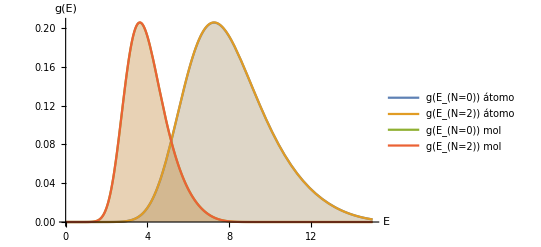

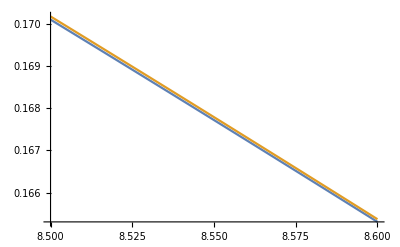

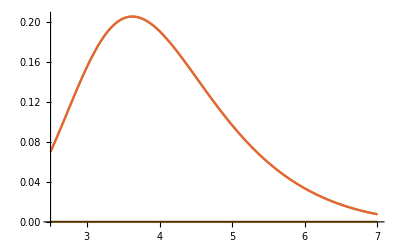

-Graphics-

-Graphics-